```mathematica
Clear[F,G,p,R,Cost];
F[a_,k_]:=F[a,k]=Piecewise[{{1-∑_(n=0)^(k-1) 1/(n!)*(a/μ)^n*Exp[-a/μ], a>0}, {0, a==0}}];
G[a_,k_]:=G[a,k]=Piecewise[{{μ*k*F[a,k+1]/F[a,k], a>0}, {0, a==0}}];
p[a_,k_,j_]:=p[a,k,j]=Piecewise[{{Boole[j==k+1], a==0}, {Boole[j==1], a>0&&k==0}, {F[a,k], a>0&&k≥1&&j==1}, {F[a,k-(j-1)]-F[a,k-(j-1)+1], a>0&&k≥1&&2≤j&&j≤k}, {1-F[a,1], a>0&&k≥1&&j==(k+1)}, {0, True}}];
R[a_,k_,j_]:=R[a,k,j]=Piecewise[{{0, a==0}, {cI*a+(G[a,k]*(cW*(k+1)-2*cI))/2, a>0&&k≥0&&j==1}, {cW*a*(j-1)+(cW*G[a,k-(j-1)]*(k-(j-1)+1))/2, a>0&&k≥1&&2≤j&&j≤(k+1)}}];
Cost[a_,n_,k_]:=Cost[a,n,k]=∑_(j=1)^(k+1) p[a,k,j]*(R[a,k,j]+OptimalCost[n-1,j]);
```

```mathematica
Clear[Optimal];
Optimal[n_,k_]:=Optimal[n,k]=NMinimize[{Cost[a,n,k],a≥0},a];
```

```mathematica
Clear[OptimalCost,OptimalTime];
OptimalCost[n_,k_]:=OptimalCost[n,k]=Piecewise[{{(cW*μ*k*(k+1))/2, n==0}, {First[Optimal[n,k]], n≥1}}];
OptimalTime[n_,k_]:=OptimalTime[n,k]=a/.Last[Optimal[n,k]];
```

```mathematica
μ=1;
cW=1;
cI=1;
```

```mathematica
num=8;
Table[OptimalCost[n,0],{n,0,num}]
Table[Table[If[n+k≤num,OptimalCost[n,k],0],{k,0,num}],{n,0,num}]//MatrixForm
Table[Table[If[n+k≤num,OptimalTime[n,k],0],{k,0,num}],{n,1,num}]//MatrixForm
```

{0,1.,2.69315,4.52005,6.35018,8.18013,10.0101,11.84,13.6699}

(0 | 1 | 3 | 6 | 10 | 15 | 21 | 28 | 36
1. | 2.69315 | 4.97937 | 8.04949 | 11.9605 | 16.7418 | 22.4099 | 28.9754 | 0
2.69315 | 4.52005 | 6.81367 | 9.88121 | 13.7875 | 18.5622 | 24.2216 | 0 | 0
4.52005 | 6.35018 | 8.64338 | 11.7105 | 15.6165 | 20.3907 | 0 | 0 | 0
6.35018 | 8.18013 | 10.4733 | 13.5404 | 17.4463 | 0 | 0 | 0 | 0
8.18013 | 10.0101 | 12.3032 | 15.3703 | 0 | 0 | 0 | 0 | 0
10.0101 | 11.84 | 14.1331 | 0 | 0 | 0 | 0 | 0 | 0
11.84 | 13.6699 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13.6699 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0. | 0.693147 | 1.75711 | 2.82577 | 3.85505 | 4.8492 | 5.81636 | 6.76318 | 0
0. | 0.826902 | 1.90223 | 2.95223 | 3.95872 | 4.92979 | 5.87421 | 0 | 0
0. | 0.83013 | 1.90481 | 2.95403 | 3.9598 | 4.93022 | 0 | 0 | 0
0. | 0.82995 | 1.90455 | 2.95373 | 3.95948 | 0 | 0 | 0 | 0
0. | 0.829925 | 1.90452 | 2.95369 | 0 | 0 | 0 | 0 | 0
0. | 0.829923 | 1.90451 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0.829923 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

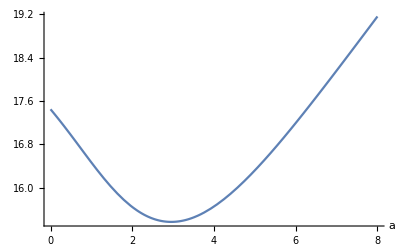

```mathematica
Plot[Cost[a,5,3],{a,0,8},AxesLabel->Automatic]
```